```mathematica
ResourceFunction["MaTeXInstall"][];
ConfigureMaTeX["Ghostscript"->"C:\\Program Files\\gs\\gs10.03.0\\bin\\gswin64c.exe"];
ConfigureMaTeX["pdfLaTeX" -> "C:\\texlive\\2024\\bin\\windows\\pdflatex.exe"];
<<MaTeX`;
MaTeX["x^2"] (*Este bloque echa a andar MaTeX. Para tener tipografia tipo LaTeX*)
```

-Graphics-

```mathematica
(*Parametros*)
ν=1/3;
a = 0.01;
aPrime = 0.01;
```

```mathematica
coeficienteB[ω_, k_]:=-(ω+(1-ν)k^2 Cosh[(√(ω+k^2))/2])/(ω-(1-ν)k^2 Cos[(√(ω+k^2))/2])*a;
coeficienteBPrima[ω_, k_]:=-(ω+(1-ν)k^2 Sinh[(√(ω+k^2))/2])/(ω-(1-ν)k^2 Sin[(√(ω+k^2))/2])*aPrime;
frecuenciaωSimPositivo[waveNumber_, offset_]:= Re[w/.First[With[{k=waveNumber}, FindRoot[Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Cosh[Sqrt[w+k^2]/2]*Sin[Sqrt[w-k^2]/2]+
Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Sinh[Sqrt[w+k^2]/2]*Cos[Sqrt[w-k^2]/2]==0,{w,Abs[k]^2+offset}, WorkingPrecision->MachinePrecision]]]];
frecuenciaωAntiSimPositivo[waveNumber_, offset_]:= Re[w/.First[With[{k=waveNumber}, FindRoot[Sqrt[w+k^2]*(w-(1-ν)k^2)^2 *Tan[Sqrt[w-k^2]/2]-
Sqrt[w-k^2]*(w+(1-ν)k^2)^2 *Tanh[Sqrt[w+k^2]/2]==0,{w,Abs[k]+offset}]]]];
frecuenciaωAntiSimPositivo[0.1, 60]
```

61.6871

```mathematica
amplitudWSim[k_,y_,off_]:=Re[a*Cosh[√(frecuenciaωSimPositivo[k, off]+k^2)*y]+coeficienteB[frecuenciaωSimPositivo[k, off],k]*Cos[√(frecuenciaωSimPositivo[k, off]-k^2)*y]];
amplitudWAntiSim[k_,y_,off_]:=aPrime*Sinh[√(frecuenciaωAntiSimPositivo[k, off]+k^2)*y];
```

```mathematica
amplitudWAntiSim[0.1, 0.5, 60]
```

0.253769

```mathematica
DisplacementSim[k_,x_,y_,t_, off_]:=Re[amplitudWSim[k,y, off]*Exp[I*(k*x-frecuenciaωSimPositivo[k, off]*t)]];

DisplacementAntiSim[k_,x_,y_,t_, off_]:=Re[amplitudWAntiSim[k,y,off]*Exp[I*(k*x-frecuenciaωAntiSimPositivo[k,off]*t)]];
DisplacementAntiSim[0.1, 0, 0.2, 0, 60]
```

0.0230168

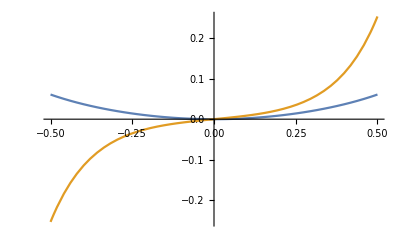

```mathematica
Plot[{DisplacementSim[0.1,0.0,y,0.0,30], DisplacementAntiSim[0.1,0.0,y,0.0, 60]},{y,-0.5,0.5}, PlotRange->All]
```

```mathematica
Manipulate[Plot3D[DisplacementSim[0.1,x,y,t,0], {x,-50,50},{y,-0.5,0.5}],{t,0.0, 1000.0}]
```

```mathematica
Export["oscilacionSimetrica.gif",%]
```

oscilacionSimetrica.gif

```mathematica
Manipulate[Plot3D[DisplacementAntiSim[0.1,x,y,t, 60], {x,-20,20},{y,-0.5,0.5}],{t,0.0, 1000.0}]
```

```mathematica
Export["oscilacionAntisimetrica.gif",%]
```

oscilacionAntisimetrica.gif

```mathematica
simetricWaveFront=Plot3D[DisplacementSim[0.1,x,y,0.0,0], {x,-50,50},{y,-0.5,0.5}, ImageSize->Large,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
AxesLabel->{
MaTeX["x/W", Magnification->2], 
MaTeX["y/W", Magnification->2],MaTeX["z/W", Magnification->2]}
]
```

-Graphics3D-

```mathematica
Export["simmetricWaveFront.pdf",simetricWaveFront]
```

simmetricWaveFront.pdf

```mathematica
AntisimetricWaveFront=Plot3D[DisplacementAntiSim[0.1,x,y,0.0,0.0], {x,-50,50},{y,-0.5,0.5}, ImageSize->Large,
LabelStyle->{FontFamily->"CMU Serif", FontSize->20}, 
AxesLabel->{
MaTeX["x/W", Magnification->2], 
MaTeX["y/W", Magnification->2],MaTeX["z/W", Magnification->2]}
]
```

-Graphics3D-

```mathematica
Export["AntisimmetricWaveFront.pdf",AntisimetricWaveFront]
```

AntisimmetricWaveFront.pdf